## POSIT

### POSIT routines

```mathematica
GetPOSIT[imagePoints_,objectPoints_,objectMatrix_,focalLength_]:=Module[{objectVectors,imageVectors,IVect,JVect,ISquare,JSquare,IJ,imageDifference,row1,row2,row3,scale1,scale2,scale,oldSOPImagePoints,SOPImagePoints,translation,rotation,count=0,converged=False,u2,u3},
objectVectors=(#-objectPoints[[1]])&/@objectPoints;
oldSOPImagePoints=imagePoints;
(* loop until difference between 2 SOP images is less than one pixel *)
While[!converged,
If[count==0,
(* we get image vectors from image of reference point for POS: *)
imageVectors=Map[(#-imagePoints[[1]])&,imagePoints],
(* else count>0 , we compute a SOP image first for POSIT: *)
SOPImagePoints=imagePoints(1+(objectVectors.row3)/translation[[3]]);
imageDifference=Apply[Plus,Abs[Round[Flatten[SOPImagePoints]]-Round[Flatten[oldSOPImagePoints]]]];
oldSOPImagePoints=SOPImagePoints;
imageVectors=Map[(#-SOPImagePoints[[1]])&,SOPImagePoints]
];(*End If*)
{IVect,JVect}=Transpose[objectMatrix.imageVectors];
ISquare=IVect.IVect;JSquare=JVect.JVect;IJ=IVect.JVect;
{scale1,scale2}=Sqrt[{ISquare,JSquare}];
{row1,row2}={IVect/scale1,JVect/scale2};
(*row3=RotateLeft[row1] RotateRight[row2]-RotateLeft[row2] RotateRight[row1];(*cross-product*)*)
row3=row1×row2;
(*Orthogonalization*)
u2=Normalize[row2-(row2.row1)row1];
u3=Normalize[row3-(row3.row1)row1-(row3.row2)row2];
rotation={row1,u2,u3};
scale=(scale1+scale2)/2.0;(*scaling factor in SOP*)
translation=Append[imagePoints[[1]],focalLength]/scale;
converged=(count>0)&&(imageDifference<1);
count++];(*End While*)
Return[{rotation,translation}]] (*End Module*)
```

```mathematica
GetPOSITNonOrtho[imagePoints_,objectPoints_,objectMatrix_,focalLength_]:=Module[{objectVectors,imageVectors,IVect,JVect,ISquare,JSquare,IJ,imageDifference,row1,row2,row3,scale1,scale2,scale,oldSOPImagePoints,SOPImagePoints,translation,rotation,count=0,converged=False,rotations,translations},
objectVectors=(#-objectPoints[[1]])&/@objectPoints;
oldSOPImagePoints=imagePoints;
(* loop until difference between 2 SOP images is less than one pixel *)
While[!converged,
If[count==0,
(* we get image vectors from image of reference point for POS: *)
imageVectors=Map[(#-imagePoints[[1]])&,imagePoints],
(* else count>0 , we compute a SOP image first for POSIT: *)
SOPImagePoints=imagePoints(1+(objectVectors.row3)/translation[[3]]);
imageDifference=Apply[Plus,Abs[Round[Flatten[SOPImagePoints]]-Round[Flatten[oldSOPImagePoints]]]];
oldSOPImagePoints=SOPImagePoints;
imageVectors=Map[(#-SOPImagePoints[[1]])&,SOPImagePoints]
];(*End If*)
{IVect,JVect}=Transpose[objectMatrix.imageVectors];
ISquare=IVect.IVect;JSquare=JVect.JVect;IJ=IVect.JVect;
{scale1,scale2}=Sqrt[{ISquare,JSquare}];
{row1,row2}={IVect/scale1,JVect/scale2};
row3=RotateLeft[row1] RotateRight[row2]-RotateLeft[row2] RotateRight[row1];(*cross-product*)
rotation={row1,row2,row3};
scale=(scale1+scale2)/2.0;(*scaling factor in SOP*)
translation=Append[imagePoints[[1]],focalLength]/scale;
converged=(count>0)&&(imageDifference<1);
count++];(*End While*)
Return[{rotation,translation}]] (*End Module*)
```

```mathematica
GetPOSITAll[imagePoints_,objectPoints_,objectMatrix_,focalLength_]:=Module[{objectVectors,imageVectors,IVect,JVect,ISquare,JSquare,IJ,imageDifference,row1,row2,row3,scale1,scale2,scale,oldSOPImagePoints,SOPImagePoints,translation,rotation,count=0,converged=False,rotations,translations},
objectVectors=(#-objectPoints[[1]])&/@objectPoints;
oldSOPImagePoints=imagePoints;
rotations={};translations={};
(* loop until difference between 2 SOP images is less than one pixel *)
While[!converged,
If[count==0,
(* we get image vectors from image of reference point for POS: *)
imageVectors=Map[(#-imagePoints[[1]])&,imagePoints],
(* else count>0 , we compute a SOP image first for POSIT: *)
SOPImagePoints=imagePoints(1+(objectVectors.row3)/translation[[3]]);
imageDifference=Apply[Plus,Abs[Round[Flatten[SOPImagePoints]]-Round[Flatten[oldSOPImagePoints]]]];
oldSOPImagePoints=SOPImagePoints;
imageVectors=Map[(#-SOPImagePoints[[1]])&,SOPImagePoints]
];(*End If*)
{IVect,JVect}=Transpose[objectMatrix.imageVectors];
ISquare=IVect.IVect;JSquare=JVect.JVect;IJ=IVect.JVect;
{scale1,scale2}=Sqrt[{ISquare,JSquare}];
{row1,row2}={IVect/scale1,JVect/scale2};
row3=RotateLeft[row1] RotateRight[row2]-RotateLeft[row2] RotateRight[row1];(*cross-product*)
rotation={row1,row2,row3};
scale=(scale1+scale2)/2.0;(*scaling factor in SOP*)
translation=Append[imagePoints[[1]],focalLength]/scale;
converged=(count>0)&&(imageDifference<1);
AppendTo[rotations,rotation];AppendTo[translations,translation];
count++];(*End While*)
Return[{rotations,translations}]] (*End Module*)
```

### Focal length calc

```mathematica
hFOV=42°;
vFOV=32°;
```

```mathematica
Tan[hFOV/2]//N
```

0.383864

```mathematica
20/(2Tan[hFOV/2])//N
```

26.0509

```mathematica
Solve[h/(2 f)==Tan[hFOV/2],f]//N
```

{{f→1.30254 h}}

### Test cube

```mathematica
focLength=760;
cube={{0,0,0},{10,0,0},{10,10,0},{0,10,0},{0,0,10},{10,0,10},{10,10,10},{0,10,10}};
cubeMatrix=PseudoInverse[cube]//N;
cubeImage={{0,0},{80,-93},{245,-77},{185,32},{32,135},{99,35},{247,62},{195,179}};
```

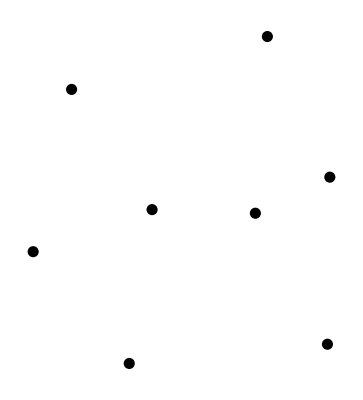

```mathematica
Graphics[{PointSize[0.02],Point/@cubeImage}]
```

```mathematica
{POSITr,POSITt}=GetPOSIT[cubeImage,cube,cubeMatrix,focLength]
```

{{{0.490101,0.850566,0.190625},{-0.569415,0.146829,0.808831},{0.659975,-0.504954,0.556286}},{0.,0.,40.0264}}

```mathematica
GetPOSITAll[cubeImage,cube,cubeMatrix,focLength]
```

{{{{0.379852,0.917529,0.117701},{-0.587476,0.177808,0.789466},{0.70343,-0.369026,0.606567}},{{0.476662,0.859351,0.185228},{-0.569972,0.152834,0.807325},{0.665467,-0.490395,0.562656}},{{0.492453,0.848737,0.192706},{-0.568872,0.146332,0.809303},{0.658686,-0.508169,0.554884}},{{0.490928,0.849986,0.191086},{-0.569394,0.146415,0.808921},{0.659594,-0.505925,0.555856}},{{0.490104,0.850571,0.190595},{-0.569498,0.146689,0.808798},{0.659982,-0.504939,0.556292}},{{0.490072,0.850588,0.190605},{-0.569489,0.146717,0.808799},{0.659989,-0.504917,0.556303}},{{0.490101,0.850566,0.190625},{-0.569484,0.146709,0.808804},{0.659975,-0.504954,0.556286}}},{{0.,0.,41.9117},{0.,0.,38.7577},{0.,0.,39.7905},{0.,0.,40.0518},{0.,0.,40.0392},{0.,0.,40.0272},{0.,0.,40.0264}}}

```mathematica
Graphics3D[{Red,PointSize[0.02],Point/@(POSITr.#&/@cube)},ViewPoint->{0,0,focLength},ViewVertical->{0,-1, 0}]
```

-Graphics3D-

```mathematica
Graphics[{PointSize[0.02],Point/@cubeImage}]
```

-Graphics-

## Another Test

```mathematica
Hx=1;Hy=3;Hz=2;
object={{0,0,0},{Hx,0,0},{0,Hy,0},{0,0,Hz}};
objectMatrix=PseudoInverse[object]
colors={Black,Red,Green,Blue};
colorsRep=Darker/@{Black,Red,Green,Blue};
Graphics3D[{PointSize[0.02],{#⟦1⟧,Point[#⟦2⟧]}&/@Partition[Riffle[colors,object],2]}];
```

{{0,1,0,0},{0,0,1/3,0},{0,0,0,1/2}}

### TODO/NOTE: GetPositALL-ban nincs orthogonalizáció

```mathematica
GetPOSIT[{{0,0},{100,0},{20,30},{0,100}},object,objectMatrix,focLength][[1]]//N
```

{{0.998916,0.0465525,0.},{-0.00630066,0.135199,0.990798},{0.0461241,-0.989724,0.135345}}

```mathematica
GetPOSITAll[{{0,0},{100,0},{20,30},{0,100}},object,objectMatrix,focLength][[1,-1]]//N
```

{{0.998916,0.0465525,0.},{0.,0.13549,0.990779},{0.0461232,-0.989705,0.135343}}

```mathematica
DrawPoints[colors_,points_]:={#⟦1⟧,Point[#⟦2⟧]}&/@Partition[Riffle[colors,points],2]
DrawLines[colors_,points_]:=Table[{colors⟦i⟧,Line[{points⟦1⟧,points⟦i⟧}]},{i,2,Length@points}]
```

```mathematica
textS=Directive[Black, 12,FontFamily->"CMU Serif"];
pR=15;
Manipulate[
Module[{R,T,locR},
{R,T}=GetPOSIT[{loc1,loc2,loc3,loc4},object,objectMatrix,focLength];
locR=R.#&/@object;
Row[{
Graphics[{PointSize[0.02],DrawPoints[colors,{loc1,loc2,loc3,loc4}],DrawLines[colors,{loc1,loc2,loc3,loc4}]},
ImageSize->500,Axes->True,AxesLabel->{"IMGx","IMGy"},PlotRange->{{0,110},{0,110}},PlotLabel->"Input 2D points",LabelStyle->textS,AxesStyle->textS],
Graphics3D[{PointSize[0.02],DrawPoints[colors,locR],DrawLines[colors,locR],White,Opacity[0.4],GeometricTransformation[Cuboid[{0,0,0},{Hx,Hy,Hz}],R]},
ImageSize->500,Axes->True,AxesLabel->{"x","y","z"},ViewPoint->{0,0,5},PlotLabel->Row[{MatrixPlot[Transpose[R].R,ColorFunction->Hue]," ",PaddedForm[MatrixForm[Chop[Transpose[R].R]],{1,3}]}],LabelStyle->textS,AxesStyle->textS,PlotRange->4{{-1,1},{-1,1},{-1,1}}]
}]
],
{{loc1,{70,30}},Locator},
{{loc2,{95,40}},Locator},
{{loc3,{0,40}},Locator},
{{loc4,{70,65}},Locator}
];
```

### Object parameters

```mathematica
objectPar={{0,0,0},{HX,0,0},{0,HY,0},{0,0,HZ}};
objectPar//MatrixForm
```

(0 | 0 | 0
HX | 0 | 0
0 | HY | 0
0 | 0 | HZ)

```mathematica
PseudoInverse[objectPar]//MatrixForm
```

(0 | 1/HX | 0 | 0
0 | 0 | 1/HY | 0
0 | 0 | 0 | 1/HZ)

```mathematica
objectPar2={{0,0,0},{Ax,0,0},{Bx,By,Bz},{Cy,Cy,Cz}};
objectPar2//MatrixForm
```

(0 | 0 | 0
Ax | 0 | 0
Bx | By | Bz
Cy | Cy | Cz)

## Reprojection

```mathematica
testPoints={{70,30},{95,40},{0,40},{70,65}};
focLength=760;
```

```mathematica
pose=GetPOSIT[testPoints,object,objectMatrix,focLength]
```

{{{0.699546,-0.713965,0.0298291},{0.274493,0.307021,0.911258},{-0.659764,-0.629279,0.410753}},{2.62361,1.1244,28.4849}}

```mathematica
reproj=((pose[[1]].#)[[1;;2]]*pose[[2,3]]+testPoints[[1]]&/@object)
Point/@reproj//Graphics
```

{{70.,30.},{89.9265,37.8189},{8.98844,56.2364},{71.6994,81.9141}}

-Graphics-

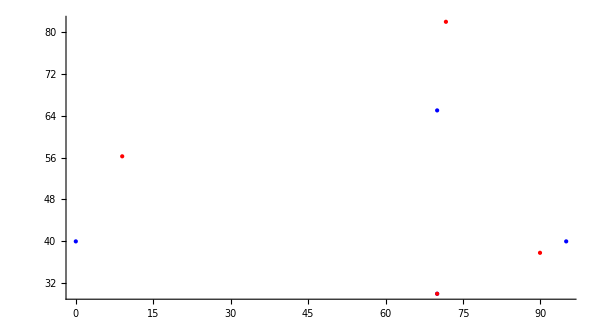

```mathematica
Graphics[{Blue,Point/@testPoints,
Red,Point/@reproj},Axes->True,ImageSize->600]
```

## Initial point correspondence

```mathematica
DrawPoints[colors_,points_]:={#⟦1⟧,Point[#⟦2⟧]}&/@Partition[Riffle[colors,points],2]
DrawLines[colors_,points_]:=Table[{colors⟦i⟧,Line[{points⟦1⟧,points⟦i⟧}]},{i,2,Length@points}]
```

```mathematica
testPoints={{70,30},{95,40},{0,40},{70,65}}
```

{{70,30},{95,40},{0,40},{70,65}}

```mathematica
targetRMX=GetPOSIT[testPoints,object,objectMatrix,focLength][[1]]
```

{{0.699546,-0.713965,0.0298291},{0.274493,0.307021,0.911258},{-0.659764,-0.629279,0.410753}}

```mathematica
scrambled=testPoints[[{2,4,3,1}]]
```

{{95,40},{70,65},{0,40},{70,30}}

```mathematica
moved=RandomInteger[{-10,10},2]+#&/@scrambled
```

{{100,32},{77,69},{6,39},{61,33}}

```mathematica
GetPointCorrespondence[points_,targetRMX_]:=Module[{indices,ptsPermutations,RMXlist,Elist,bestIndices,bestError},
indices=Permutations[{1,2,3,4}];
ptsPermutations=Part[points,#]&/@indices;
RMXlist=GetPOSIT[#,object,objectMatrix,focLength][[1]]&/@ptsPermutations;
Elist=(Total@Diagonal[Transpose[targetRMX].#]/3)&/@RMXlist;
{bestIndices,bestError}=SortBy[Transpose@{indices,Elist},Last][[-1]];
GetPOSIT[points[[bestIndices]],object,objectMatrix,focLength]~Join~{bestIndices,bestError}
]
```

```mathematica
GetPointCorrespondence[moved,targetRMX]
```

{{{0.879119,-0.43788,0.188175},{-0.172131,0.0764655,0.982102},{-0.444432,-0.895775,-0.00815071}},{2.01962,1.09258,25.1624},{4,1,3,2},0.88599}

```mathematica
Transpose[#].#&@(GetPOSIT[testPoints,object,objectMatrix,focLength][[1]])
```

{{1.,5.55112×10^-17,-5.55112×10^-17},{5.55112×10^-17,1.,-5.55112×10^-17},{-5.55112×10^-17,-5.55112×10^-17,1.}}

```mathematica
Transpose[#].#&@(GetPOSITNonOrtho[testPoints,object,objectMatrix,focLength][[1]])
```

{{1.09129,-0.0573923,0.158283},{-0.0573923,0.89549,-0.157321},{0.158283,-0.157321,0.951227}}

```mathematica
Transpose[(GetPOSIT[testPoints,object,objectMatrix,focLength][[1]])].(GetPOSITNonOrtho[testPoints,object,objectMatrix,focLength][[1]])-IdentityMatrix[3]
```

{{0.0317289,-0.0645244,0.0026958},{0.0377468,-0.0700173,0.00160954},{0.159377,-0.162661,-0.0246966}}

Ehhez kell valami okos teszt!

```mathematica
GetPointCorrespondenceAuto[points_]:=Module[{indices,ptsPermutations,RMXlist,RMXnoList,Elist,bestIndices,bestError},
indices=Permutations[{1,2,3,4}];
ptsPermutations=Part[points,#]&/@indices;
RMXnoList=GetPOSITNonOrtho[#,object,objectMatrix,focLength][[1]]&/@ptsPermutations;
RMXlist=GetPOSIT[#,object,objectMatrix,focLength][[1]]&/@ptsPermutations;
Elist=Table[Norm[Diagonal[Transpose[RMXlist[[i]]].RMXnoList[[i]]]-{1,1,1}],{i,1,Length@ptsPermutations}];
{bestIndices,bestError}=SortBy[Transpose@{indices,Elist},Last][[1]];
GetPOSIT[points[[bestIndices]],object,objectMatrix,focLength]~Join~{bestIndices,bestError}
]
```

```mathematica
GetPointCorrespondenceAuto[scrambled]
```

{{{0.892309,0.237624,0.383823},{-0.121486,0.945282,-0.302792},{-0.434772,0.223554,0.872352}},{0.,0.708032,13.4526},{3,1,2,4},0.00257288}

```mathematica
GetPointCorrespondenceAuto[moved]
```

{{{0.879119,-0.43788,0.188175},{-0.172131,0.0764655,0.982102},{-0.444432,-0.895775,-0.00815071}},{2.01962,1.09258,25.1624},{4,1,3,2},0.0216853}

```mathematica
textS=Directive[Black, 12,FontFamily->"CMU Serif"];
pR=15;
Manipulate[
Module[{R,T,locR,rep,corr1,corr2},
{R,T}=GetPOSIT[{loc1,loc2,loc3,loc4},object,objectMatrix,focalLen];
rep=((R.#)[[1;;2]]*T[[3]]+loc1&/@object);
locR=R.#&/@object;
corr1=GetPointCorrespondence[RandomInteger[{-5,5},2]+#&/@{loc1,loc2,loc3,loc4},R];
corr2=GetPointCorrespondenceAuto[{loc1,loc2,loc3,loc4}];
Row[{
Graphics[{PointSize[0.02],DrawPoints[colors,{loc1,loc2,loc3,loc4}],DrawLines[colors,{loc1,loc2,loc3,loc4}],DrawPoints[colorsRep,rep],DrawLines[colorsRep,rep]},
ImageSize->500,Axes->True,AxesLabel->{"IMGx","IMGy"},PlotRange->{{0,110},{0,110}},LabelStyle->textS,AxesStyle->textS,
PlotLabel->Column[{"Input 2D points",Row@{"Pt correspondence: ",corr1[[3]]},Row@{"Pt correspondence (auto): ",corr2[[3]]}}]],
Graphics3D[{PointSize[0.02],DrawPoints[colors,locR],DrawLines[colors,locR],White,Opacity[0.4],GeometricTransformation[Cuboid[{0,0,0},{Hx,Hy,Hz}],{R,T}]},
ImageSize->500,Axes->True,AxesLabel->{"x","y","z"},ViewPoint->{0,0,5},PlotLabel->Row[{Transpose@{T}," ",MatrixPlot[R,ColorFunction->Hue]," ",PaddedForm[MatrixForm[Chop[R]],{1,3}]," ",Transpose@{EulerAngles[R]}}],LabelStyle->textS,AxesStyle->textS,PlotRange->4{{-1,1},{-1,1},{-1,1}}]
}]
],
{{loc1,{70,30}},Locator},
{{loc2,{90,40}},Locator},
{{loc3,{15,50}},Locator},
{{loc4,{70,80}},Locator},
{{focalLen,720},120,1000,Appearance->"Labeled"}
]
```